```mathematica
rts = {1.998396, 1.030533, 0.703248, 0.536062, 0.476404, 0.414597, 0.388929, 0.383223};
rts = rts⟦1⟧ / rts;
```

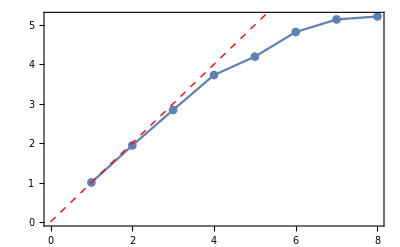

```mathematica
Show[
ListPlot[rts, Joined->True, PlotMarkers->Automatic, Frame->True, FrameStyle->Thick, ImageSize->400],
Plot[x, {x, 0, 8}, PlotStyle->{Thick, Dashed, Red}]
]
```